```mathematica
Clear["Global`*"]
```

```mathematica
Q0start=54953.53841518038;Q0end=54963.24481732253;
Q1start=54964.511756673426;Q1end=54997.98329729108;
Q2start=55002.764903284085;Q2end=55091.466956257034;
Q3start=55093.24459723139;Q3end=55182.49465072287;
Q4start=55185.3658080061;Q4end=55275.211866897414;
Q5start=55276.47949780036;Q5end=55371.17207391215;
Q6start=55372.46009847967;Q6end=55462.305792973355;
Q7start=55463.16463513537;Q7end=55552.55707265549;
Q8start=55568.35242605389;Q8end=55635.35368505794;
Q9start=55641.52550915837;Q9end=55738.935875129384;
Q10start=55739.835638486584;Q10end=55833.277845301614;
Q11start=55834.1986379302;Q11end=55931.33445044336;
Q12start=55932.418064826525;Q12end=56015.03062305053;
Q13start=56015.72674011688;Q13end=56106.066162428935;
Q14start=56107.13008618061;Q14end=56204.331588511515;
Q15start=56206.50817485861;Q15end=56304.13718779086;
Q16start=56305.08740097;Q16end=56390.96969746;Q17start=56391;Q17end=57000;
quack={{Q0start,Q1end,1},{Q2start,Q2end,2},{Q3start,Q3end,3},{Q4start,Q4end,4},{Q5start,Q5end,5},{Q6start,Q6end,6},{Q7start,Q7end,7},{Q8start,Q8end,8},{Q9start,Q9end,9},{Q10start,Q10end,10},{Q11start,Q11end,11},{Q12start,Q12end,12},{Q13start,Q13end,13},{Q14start,Q14end,14},{Q15start,Q15end,15},{Q16start,Q16end,16},{Q17start,Q17end,17}};
quarterfind[t_]:=Select[quack,#[[1]]<t<#[[2]]&][[1,3]];
```

## start here

```mathematica
thisfolder=NotebookDirectory[]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/LIGHTCURVES3/SINGLES/KOI-5033.01/planet1/

```mathematica
type="NEA";
planetnumber=ToExpression[Last[Characters[StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-0]]]]];
kic=StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-1]];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-1]];
Clear[temp];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-2]];
j=0;rootfolder="/";Label[jloop];j=j+1;rootfolder=StringJoin[rootfolder,temp[[j]],"/"];If[j<Length[temp],Goto[jloop]]
Clear[temp];
```

### compile file names

```mathematica
cofiamfiles=FileNames[StringJoin[thisfolder,"SAP/cofiam*.dat"]];
localfiles=FileNames[StringJoin[thisfolder,"SAP/local*.dat"]];
polyamfiles=FileNames[StringJoin[thisfolder,"SAP/polyam*.dat"]];
gpfiles=FileNames[StringJoin[thisfolder,"SAP/gp*.dat"]];
cofiamfiles2=FileNames[StringJoin[thisfolder,"PDC/cofiam*.dat"]];
localfiles2=FileNames[StringJoin[thisfolder,"PDC/local*.dat"]];
polyamfiles2=FileNames[StringJoin[thisfolder,"PDC/polyam*.dat"]];
gpfiles2=FileNames[StringJoin[thisfolder,"PDC/gp*.dat"]];
```

```mathematica
epochs=Union[Join[StringSplit[cofiamfiles,"."][[All,3]],StringSplit[localfiles,"."][[All,3]],StringSplit[polyamfiles,"."][[All,3]],StringSplit[gpfiles,"."][[All,3]],StringSplit[cofiamfiles2,"."][[All,3]],StringSplit[localfiles2,"."][[All,3]],StringSplit[polyamfiles2,"."][[All,3]],StringSplit[gpfiles2,"."][[All,3]]]];
```

```mathematica
cofiamgiles=Table[StringJoin[thisfolder,"SAP/cofiamSAP.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
localgiles=Table[StringJoin[thisfolder,"SAP/localSAP.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
polyamgiles=Table[StringJoin[thisfolder,"SAP/polyamSAP.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
gpgiles=Table[StringJoin[thisfolder,"SAP/gpSAP.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
cofiamgiles2=Table[StringJoin[thisfolder,"PDC/cofiamPDC.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
localgiles2=Table[StringJoin[thisfolder,"PDC/localPDC.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
polyamgiles2=Table[StringJoin[thisfolder,"PDC/polyamPDC.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
gpgiles2=Table[StringJoin[thisfolder,"PDC/gpPDC.",epochs[[i]],".dat"],{i,1,Length[epochs]}];
```

### import SAP

```mathematica
"cofiam";
j=0;Label[jloop];j=j+1;thisfile=cofiamgiles[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];Subscript[cofiam, j]=Import[thisfile,"Table"];Label[endbit];If[!FileExistsQ[thisfile],Subscript[cofiam, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local";
j=0;Label[jloop];j=j+1;thisfile=localgiles[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];Subscript[local, j]=Import[thisfile,"Table"];Label[endbit];If[!FileExistsQ[thisfile],Subscript[local, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam";
j=0;Label[jloop];j=j+1;thisfile=polyamgiles[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];Subscript[polyam, j]=Import[thisfile,"Table"];Label[endbit];If[!FileExistsQ[thisfile],Subscript[polyam, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp";
j=0;Label[jloop];j=j+1;thisfile=gpgiles[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];Subscript[gp, j]=Import[thisfile,"Table"];Label[endbit];If[!FileExistsQ[thisfile],Subscript[gp, j]={}];If[j<Length[epochs],Goto[jloop]];
```

### import & correct PDC files

```mathematica
blends=Flatten[Import[StringJoin[thisfolder,"blends.dat"],"Table"]];
```

```mathematica
"cofiam";
j=0;Label[jloop];j=j+1;thisfile=cofiamgiles2[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];thisdata=Import[thisfile,"Table"];thisquarter=quarterfind[Median[thisdata[[All,1]]]];thisblend=1.0/blends[[thisquarter]];newdata=Table[{thisdata[[i,1]],(thisdata[[i,2]]+(thisblend-1))/thisblend,thisdata[[i,3]]},{i,1,Length[thisdata]}];Subscript[cofiam2, j]=newdata;Label[endbit];If[!FileExistsQ[thisfile],Subscript[cofiam2, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local";
j=0;Label[jloop];j=j+1;thisfile=localgiles2[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];thisdata=Import[thisfile,"Table"];thisquarter=quarterfind[Median[thisdata[[All,1]]]];thisblend=1.0/blends[[thisquarter]];newdata=Table[{thisdata[[i,1]],(thisdata[[i,2]]+(thisblend-1))/thisblend,thisdata[[i,3]]},{i,1,Length[thisdata]}];Subscript[local2, j]=newdata;Label[endbit];If[!FileExistsQ[thisfile],Subscript[local2, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam";
j=0;Label[jloop];j=j+1;thisfile=polyamgiles2[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];thisdata=Import[thisfile,"Table"];thisquarter=quarterfind[Median[thisdata[[All,1]]]];thisblend=1.0/blends[[thisquarter]];newdata=Table[{thisdata[[i,1]],(thisdata[[i,2]]+(thisblend-1))/thisblend,thisdata[[i,3]]},{i,1,Length[thisdata]}];Subscript[polyam2, j]=newdata;Label[endbit];If[!FileExistsQ[thisfile],Subscript[polyam2, j]={}];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp";
j=0;Label[jloop];j=j+1;thisfile=gpgiles2[[j]];If[!FileExistsQ[thisfile],Goto[endbit]];thisdata=Import[thisfile,"Table"];thisquarter=quarterfind[Median[thisdata[[All,1]]]];thisblend=1.0/blends[[thisquarter]];newdata=Table[{thisdata[[i,1]],(thisdata[[i,2]]+(thisblend-1))/thisblend,thisdata[[i,3]]},{i,1,Length[thisdata]}];Subscript[gp2, j]=newdata;Label[endbit];If[!FileExistsQ[thisfile],Subscript[gp2, j]={}];If[j<Length[epochs],Goto[jloop]];
```

### bin to LC if necessary

```mathematica
"cofiam";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[cofiam, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[cofiamX, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

```mathematica
"local";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[local, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[localX, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

```mathematica
"polyam";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[polyam, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[polyamX, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

First::nofirst: {} has zero length and no first element.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

First::nofirst: {} has zero length and no first element.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
"gp";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[gp, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[gpX, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

```mathematica
"cofiam2";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[cofiam2, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[cofiam2X, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

```mathematica
"local2";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[local2, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];Print["h"];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[local2X, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

```mathematica
"polyam2";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[polyam2, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[polyam2X, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

First::nofirst: {} has zero length and no first element.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

First::nofirst: {} has zero length and no first element.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair ∞ and 0.000681115.

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
"gp2";
SCcadence=0.0006811146668042056;
k=0;Label[kloop];k=k+1;thisdata=Subscript[gp2, k];If[First[First[Position[{SCcadence,30SCcadence},First[Nearest[{SCcadence,30SCcadence},Min[Table[thisdata[[i+1,1]]-thisdata[[i,1]],{i,1,Length[thisdata]-1}]]]]]]]==1,sc=1,sc=0];If[sc==0,Goto[endloop]];t0=Min[thisdata[[All,1]]];nice2=Table[{thisdata[[i,1]],thisdata[[i,2]],thisdata[[i,3]],Round[(thisdata[[i,1]]-t0)/SCcadence]+1},{i,1,Length[thisdata]}];j=0;m=0;binsize=30;jmax=Ceiling[Max[nice2[[All,4]]]/binsize];Label[jloop];j=j+1;dummy=Select[nice2,(j-1)binsize+1≤#[[4]]≤j binsize&];If[Length[dummy]>0,m=m+1];If[Length[dummy]>0,Subscript[α, m]={Sum[dummy[[i,1]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],Sum[dummy[[i,2]] dummy[[i,3]]^-2,{i,1,Length[dummy]}]/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}],√(1/Sum[dummy[[i,3]]^-2,{i,1,Length[dummy]}])}];If[j<jmax,Goto[jloop]];nicebin=Table[Subscript[α, mm],{mm,1,m}];Label[endloop];If[sc==1,thisdata2=nicebin,thisdata2=thisdata];Subscript[gp2X, k]=thisdata2;If[k<Length[epochs],Goto[kloop]];
```

### evaluate the DW fitness of each file

```mathematica
dw[list_]:=If[Length[list]>1,Sum[(list[[i]]-list[[i-1]])^2,{i,2,Length[list]}]/Sum[(list[[i]]-1)^2,{i,1,Length[list]}],2];
```

```mathematica
infofile=Import[StringJoin[rootfolder,type,".csv"],"CSV"][[19;;All]];
kic2=ToExpression[StringSplit[StringSplit[Last[StringSplit[FileNames[StringJoin[StringReplace[NotebookDirectory[],"planet1"->"RawsLC"],"*.fits"]][[1]],"/"]],"-"][[1]],"lr"][[2]]];
infoline=Select[infofile,#[[1]]==kic2&][[planetnumber]]
period=infoline[[3]]
tau0=infoline[[6]]+54833
"read duration (only for NEA, else you'll need to mannually input";
duration=N[infoline[[9]]/24]+N[(29.4244/60)/24]
```

{3974928,K05033.01,127.672,0.00219,-0.00219,227.091,0.0123,-0.0123,2.637,0.509,-0.509}

127.672

55060.1

0.130309

```mathematica
kmax=10^4;
```

#### SAP

```mathematica
"cofiam";
j=0;Label[jloop];j=j+1;thisdata=Subscript[cofiamX, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[cofiamdwσ, j]=0,Subscript[cofiamdwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local";
j=0;Label[jloop];j=j+1;thisdata=Subscript[localX, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[localdwσ, j]=0,Subscript[localdwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam";
j=0;Label[jloop];j=j+1;thisdata=Subscript[polyamX, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[polyamdwσ, j]=0,Subscript[polyamdwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp";
j=0;Label[jloop];j=j+1;thisdata=Subscript[gpX, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[gpdwσ, j]=0,Subscript[gpdwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

#### PDC

```mathematica
"cofiam2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[cofiam2X, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[cofiam2dwσ, j]=0,Subscript[cofiam2dwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[local2X, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[local2dwσ, j]=0,Subscript[local2dwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[polyam2X, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[polyam2dwσ, j]=0,Subscript[polyam2dwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[gp2X, j];If[Length[thisdata]==0,Goto[endbit]];predata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]<-duration/2&];postdata=Select[thisdata,#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]>+duration/2&];dwnative=√((dw[predata[[All,2]]]-2)^2+(dw[postdata[[All,2]]]-2)^2);k=0;Label[kloop];k=k+1;fakepredata=Table[RandomReal[NormalDistribution[predata[[i,2]],predata[[i,3]]]],{i,1,Length[predata]}];fakepostdata=Table[RandomReal[NormalDistribution[postdata[[i,2]],postdata[[i,3]]]],{i,1,Length[postdata]}];Subscript[dwfake, k]=√((dw[fakepredata]-2)^2+(dw[fakepostdata]-2)^2);If[k<kmax,Goto[kloop]];dwfakes=Table[Subscript[dwfake, k],{k,1,kmax}];Label[endbit];If[Length[thisdata]==0,Subscript[gp2dwσ, j]=0,Subscript[gp2dwσ, j]=√2 InverseErfc[N[Length[Select[dwfakes,#>dwnative&]]/kmax]]];If[j<Length[epochs],Goto[jloop]];
```

#### DW summary

```mathematica
TableForm[Table[{j,Subscript[cofiamdwσ, j],Subscript[localdwσ, j],Subscript[polyamdwσ, j],Subscript[gpdwσ, j],Subscript[cofiam2dwσ, j],Subscript[local2dwσ, j],Subscript[polyam2dwσ, j],Subscript[gp2dwσ, j]},{j,1,Length[epochs]}]]
```

1 | 0.979162 | 0.974517 | 0 | 1.50665 | 0.595664 | 0.466022 | 0 | 0.71858
2 | 0.979162 | 0.226645 | 0 | 0.988516 | 0.839837 | 0.833257 | 0 | 0.887332
3 | 0.726063 | 0.147167 | 0 | 0.718742 | 0.947076 | 0.478914 | 0 | 0.937308
4 | 0.346323 | 0.33689 | 0 | 0.532326 | 0.119979 | 0.464765 | 0 | 0.275672
5 | 1.11745 | 0.245848 | 0 | 1.11769 | 1.22334 | 0.416697 | 0 | 1.22892
6 | 1.64485 | 1.81321 | 0 | 1.63238 | 1.63048 | 1.43812 | 0 | 1.70766
7 | 1.66157 | 1.88745 | 0 | 1.88969 | 1.9574 | 1.98092 | 0 | 1.85218
8 | 0.919565 | 0.968289 | 0 | 1.26996 | 1.5531 | 1.59864 | 0 | 1.46471
9 | 1.16826 | 1.06362 | 0 | 1.3331 | 1.3201 | 1.0245 | 0 | 1.40138

### evaluate binning fitness of each file

```mathematica
monte=10^3;
```

#### SAP

```mathematica
"cofiam";
j=0;Label[jloop];j=j+1;thisdata=Subscript[cofiamX, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[cofiambinσ, j]=0,Subscript[cofiambinσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local";
j=0;Label[jloop];j=j+1;thisdata=Subscript[localX, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[localbinσ, j]=0,Subscript[localbinσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam";
j=0;Label[jloop];j=j+1;thisdata=Subscript[polyamX, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[polyambinσ, j]=0,Subscript[polyambinσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp";
j=0;Label[jloop];j=j+1;thisdata=Subscript[gpX, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[gpbinσ, j]=0,Subscript[gpbinσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

#### PDC

```mathematica
"cofiam2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[cofiam2X, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[cofiam2binσ, j]=0,Subscript[cofiam2binσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"local2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[local2X, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[local2binσ, j]=0,Subscript[local2binσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"polyam2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[polyam2X, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[polyam2binσ, j]=0,Subscript[polyam2binσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
"gp2";
j=0;Label[jloop];j=j+1;thisdata=Subscript[gp2X, j];If[Length[thisdata]==0,Goto[endbit]];outdata=Select[thisdata,Abs[#[[1]]-tau0-period Round[(#[[1]]-tau0)/period]]>duration/2&];bmax=Round[Length[outdata]/3];b=0;Label[bloop1];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[outdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop1]];binningpattern=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[binningpattern[[i,1]]],Log[binningpattern[[i,2]]]},{i,1,Length[binningpattern]}],{x},x];realgradient=linfit["ParameterTableEntries"][[2]][[1]];k=0;Label[kloop1];k=k+1;fakeoutdata=Table[{outdata[[i,1]],RandomReal[NormalDistribution[outdata[[i,2]],outdata[[i,3]]]],outdata[[i,3]]},{i,1,Length[outdata]}];b=0;Label[bloop2];b=b+1;Subscript[β, b]={b,StandardDeviation[Table[Mean[Table[fakeoutdata[[i,2]],{i,1+(l-1)b,l b}]],{l,1,Floor[Length[outdata]/b]}]]};If[b<bmax,Goto[bloop2]];Subscript[montetab, k]=Table[Subscript[β, b],{b,1,bmax}];linfit=LinearModelFit[Table[{Log[Subscript[montetab, k][[i,1]]],Log[Subscript[montetab, k][[i,2]]]},{i,1,bmax}],{x},x];Subscript[montegradient, k]=linfit["ParameterTableEntries"][[2]][[1]];If[k<monte,Goto[kloop1]];b=0;Label[bloop3];b=b+1;temp=Table[Subscript[montetab, k][[b,2]],{k,1,monte}];Subscript[γ, b]={b,Quantile[temp,0.5-0.5Erf[2/√2]],Median[temp],Quantile[temp,0.5+0.5Erf[2/√2]]};If[b<bmax,Goto[bloop3]];quantiles=Table[Subscript[γ, b],{b,1,bmax}];montegradients=Table[Subscript[montegradient, k],{k,1,monte}];probs=Table[x,{x,0,3,0.1}];k=0;Label[kloop2];k=k+1;bracket={Quantile[montegradients,0.5-0.5Erf[probs[[k]]/√2]],Quantile[montegradients,0.5+0.5Erf[probs[[k]]/√2]]};If[bracket[[1]]<realgradient<bracket[[2]],Subscript[pass, k]=1,Subscript[pass, k]=0];If[k<Length[probs],Goto[kloop2]];temp=Table[{probs[[k]],Subscript[pass, k]},{k,1,Length[probs]}];Label[endbit];If[Length[thisdata]==0,Subscript[gp2binσ, j]=0,Subscript[gp2binσ, j]=Mean[{Max[Select[temp,#[[2]]==0&][[All,1]]],Min[Select[temp,#[[2]]==1&][[All,1]]]}]];If[j<Length[epochs],Goto[jloop]];
```

#### binning summary

```mathematica
TableForm[Table[{j,Subscript[cofiambinσ, j],Subscript[localbinσ, j],Subscript[polyambinσ, j],Subscript[gpbinσ, j],Subscript[cofiam2binσ, j],Subscript[local2binσ, j],Subscript[polyam2binσ, j],Subscript[gp2binσ, j]},{j,1,Length[epochs]}]]
```

1 | 0.35 | 0.05 | 0 | 0.45 | 0.15 | 0.75 | 0 | 0.25
2 | 0.35 | 0.25 | 0 | 2.75 | 0.15 | 0.25 | 0 | 0.35
3 | 0.05 | 0.75 | 0 | 0.05 | 0.45 | 1.45 | 0 | 0.55
4 | 0.15 | 0.15 | 0 | 0.05 | 0.55 | 0.25 | 0 | 0.65
5 | 0.25 | 0.15 | 0 | 0.45 | 0.25 | 0.05 | 0 | 0.15
6 | 0.55 | 0.35 | 0 | 0.25 | 0.45 | 0.25 | 0 | 0.35
7 | 0.05 | 0.05 | 0 | 0.05 | 0.15 | 0.15 | 0 | 0.15
8 | 0.55 | 0.75 | 0 | 0.15 | 0.35 | 0.15 | 0 | 0.15
9 | 1.45 | 0.05 | 0 | 0.45 | 0.25 | 0.25 | 0 | 0.55

### determine all times

```mathematica
dwσcutoff=2;binσcutoff=2;
j=0;Label[jloop];j=j+1;Subscript[times, j]=Union[Subscript[cofiam, j][[All,1]],Subscript[local, j][[All,1]],Subscript[polyam, j][[All,1]],Subscript[gp, j][[All,1]],Subscript[cofiam2, j][[All,1]],Subscript[local2, j][[All,1]],Subscript[polyam2, j][[All,1]],Subscript[gp2, j][[All,1]]];Subscript[powerlist, j]={{Subscript[cofiam, j],{Subscript[cofiamdwσ, j],Subscript[cofiambinσ, j],Length[Subscript[cofiam, j]]}},{Subscript[local, j],{Subscript[localdwσ, j],Subscript[localbinσ, j],Length[Subscript[local, j]]}},{Subscript[polyam, j],{Subscript[polyamdwσ, j],Subscript[polyambinσ, j],Length[Subscript[polyam, j]]}},{Subscript[gp, j],{Subscript[gpdwσ, j],Subscript[gpbinσ, j],Length[Subscript[gp, j]]}},{Subscript[cofiam2, j],{Subscript[cofiam2dwσ, j],Subscript[cofiam2binσ, j],Length[Subscript[cofiam, j]]}},{Subscript[local2, j],{Subscript[local2dwσ, j],Subscript[local2binσ, j],Length[Subscript[local, j]]}},{Subscript[polyam2, j],{Subscript[polyam2dwσ, j],Subscript[polyam2binσ, j],Length[Subscript[polyam, j]]}},{Subscript[gp2, j],{Subscript[gp2dwσ, j],Subscript[gp2binσ, j],Length[Subscript[gp2, j]]}}};Subscript[powerlist, j]=Select[Subscript[powerlist, j],#[[2]][[1]]<dwσcutoff&&#[[2]][[2]]<binσcutoff&&#[[2]][[3]]>0&][[All,1]];If[j<Length[epochs],Goto[jloop]];
Table[Dimensions[Subscript[powerlist, j]][[1]],{j,1,Length[epochs]}]
```

{6,5,6,6,6,6,6,6,6}

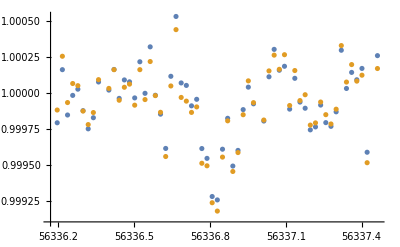

```mathematica
ListPlot[{Subscript[powerlist, j][[1]][[All,{1,2}]],Subscript[powerlist, j][[2]][[All,{1,2}]]}]
```

```mathematica
Length[Subscript[powerlist, j]]
```

6

```mathematica
Table[Length[Subscript[powerlist, j][[k]]],{k,1,Length[Subscript[powerlist, j]]}]
Length[Subscript[times2, j]]
```

{60,60,60,60,60,60}

152

```mathematica
Clear[z];j=0;Label[epochloop];j=j+1;Subscript[times2, j]=Union[Flatten[Table[Subscript[powerlist, j][[z]][[All,1]],{z,1,Length[Subscript[powerlist, j]]}]]];k=0;m=0;Label[timeloop];k=k+1;temp=Select[Flatten[Subscript[powerlist, j],1],#[[1]]==Subscript[times2, j][[k]]&];If[Length[temp]>0,m=m+1];If[Length[temp]>0,If[Length[temp[[All,2]]]>1,Subscript[avg, m]={Subscript[times2, j][[k]],Median[temp][[2]],√((Median[temp][[3]])^2+(1.4286MedianDeviation[temp][[2]])^2)},Subscript[avg, m]={Subscript[times2, j][[k]],Median[temp][[2]],Median[temp][[3]]}]];If[k<Length[Subscript[times2, j]],Goto[timeloop]];Subscript[averaged, j]=Table[Subscript[avg, kk],{kk,1,m}];If[j<Length[epochs],Goto[epochloop]];
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
j=0;Label[jloop];j=j+1;thisepoch=tau0+period Round[(Median[Subscript[averaged, j][[All,1]]]-tau0)/period];tmin=Min[Subscript[averaged, j][[All,1]]]-thisepoch;tmax=Max[Subscript[averaged, j][[All,1]]]-thisepoch;Subscript[twindow, j]=Max[-tmin,tmax];Subscript[fluxmin, j]=Min[Subscript[averaged, j][[All,2]]];Subscript[err, j]=Median[Subscript[averaged, j][[All,3]]];If[j<Length[epochs],Goto[jloop]];Twindow=Max[Table[Subscript[twindow, jj],{jj,1,Length[epochs]}]];
Fmin=Median[Select[Table[Subscript[fluxmin, jj],{jj,1,Length[epochs]}],NumberQ[#]&]];ERR=Median[Select[Table[Subscript[err, jj],{jj,1,Length[epochs]}],NumberQ[#]&]];
```

```mathematica
Table[{epochs[[jj]],Subscript[twindow, jj]},{jj,1,Length[epochs]}]
```

{{1,0.707286},{2,0.65872},{3,0.65007},{4,0.650581},{5,0.671001},{6,0.583448},{7,0.644041},{8,0.683318},{9,0.655038}}

```mathematica
j=0;Label[jloop];j=j+1;If[Length[Subscript[averaged, j]]>0,thisepoch=tau0+period Round[(Median[Subscript[averaged, j][[All,1]]]-tau0)/period]];If[Length[Subscript[averaged, j]]>0,Subscript[plotty, j]=Show[ListPlot[Subscript[cofiam, j][[All,{1,2}]],PlotRange->{{thisepoch-Twindow,thisepoch+Twindow},{1+3 ERR,Fmin-3ERR}},PlotStyle->Directive[ColorData["Rainbow"][0/7],Opacity[0.5]],Joined->True,PlotRange->All,PlotRange->{{thisepoch-Twindow,thisepoch+Twindow},{1+3 ERR,Fmin-3ERR}},Joined->True,Frame->True,AspectRatio->0.4,ImageSize->{800,Automatic},FrameLabel->{"BJKD","relative intensity"},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}],ListPlot[Subscript[local, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][1/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[polyam, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][2/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[gp, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][3/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[cofiam2, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][4/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[local2, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][5/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[polyam2, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][6/7],Opacity[0.5]],Joined->True,PlotRange->All],ListPlot[Subscript[gp2, j][[All,{1,2}]],PlotStyle->Directive[ColorData["Rainbow"][7/7],Opacity[0.5]],Joined->True,PlotRange->All],ErrorListPlot[Subscript[averaged, j],PlotRange->{{thisepoch-Twindow,thisepoch+Twindow},{1+3 ERR,Fmin-3ERR}},Joined->True,Frame->True,AspectRatio->0.4,ImageSize->{800,Automatic},FrameLabel->{"BJKD","relative intensity"},BaseStyle->{FontFamily->"CMU Serif",FontSize->22},PlotStyle->Lighter[Black]]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing,ListPlot[Subscript[averaged, j][[All,{1,2}]],PlotStyle->Lighter[Black]]]];If[Length[Subscript[averaged, j]]>0,Export[StringJoin[thisfolder,"AVG_SAP.",epochs[[j]],".pdf"],Subscript[plotty, j]]];If[Length[Subscript[averaged, j]]>0,Export[StringJoin[thisfolder,"AVG_SAP.",epochs[[j]],".dat"],Subscript[averaged, j],"Table"]];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
AVGsap=Union[Flatten[Table[Subscript[averaged, j],{j,1,Length[epochs]}],1]];
Export[StringJoin[thisfolder,"AVG_SAP.dat"],AVGsap,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/LIGHTCURVES3/SINGLES/KOI-5033.01/planet1/AVG_SAP.dat